```mathematica
(*НЕПОСРЕДСТВЕННО НАЧАЛО КУРСОВОЙ РАБОТЫ*)
```

```mathematica
(* инициализация констант*)
```

```mathematica
(*a=1;
b=2;

NN=4;
M=5;

L=4;
H=5;*)

a=0.5;
b=1.5;
NN=60;
M=30;


L=10;
H=4;


Subscript[h, r]=L/NN
Subscript[h, z]=H/M


ν=0.3;
e=17;
G=e/(2(1+ν));
δ=-0.5;

Round[Subscript[h, z]/ν,0.01]
```

1/6

2/15

0.44

```mathematica
toX[Subscript[u, i_,j_]]:=Subscript[X, (i-1)(M-1)+j];
toX[Subscript[w, i_,j_]]:=Subscript[X, (NN-1)(M-1)+(i-1)(M-1)+j];

toX[Subscript[u, i_,0]]:=0; (* СНИЗУ *)
toX[Subscript[u, 0,j_]]:=0;  (* СЛЕВА *)
toX[Subscript[u, NN,j_]]:=0;(* СПРАВА *)

toX[Subscript[w, 0,j_]]:=toX[Subscript[w, 1,j]];(* СЛЕВА *)
(*toX[Subscript[w, 0,j_]]:=Subscript[h, r](toX[Subscript[w, 1,j]]/Subscript[h, r]+(toX[Subscript[u, 0,j+1]]-toX[Subscript[u, 0,j-1]])/(2 Subscript[h, z]))*)
toX[Subscript[w, NN,j_]]:=0;(* СПРАВА *)
toX[Subscript[w, i_,0]]:=0; (* СНИЗУ *)




toX[Subscript[w, i_,M]]:=
If[ a/Subscript[h, r]≤i≤b/Subscript[h, r],-δ,
-Subscript[h, z]/(1-ν) ((1-ν)*(-toX[Subscript[w, i,M-1]])/Subscript[h, z]+ν(toX[Subscript[u, i,M]]/(i*Subscript[h, r])+(toX[Subscript[u, i+1,M]]-toX[Subscript[u, i-1,M]])/(2 Subscript[h, r])))];(* СВЕРХУ *)(* Subscript[σ, z] *)
toX[Subscript[w, i-1,M]]:=2 Subscript[h, r]((toX[Subscript[u, i,M]]-toX[Subscript[u, i_,M-1]])/Subscript[h, z]+toX[Subscript[w, i-1,M]]/(2 Subscript[h, r])) ;(* СВЕРХУ *)
(*toX[Subscript[u, i_,M]]:=toX[Subscript[u, i,M-1]];*)
(*toX[Subscript[w, i_,M]]:=If[a≤i*Subscript[h, r]≤b,
-δ,
-Subscript[h, r]/ν ((1-ν)*(toX[Subscript[u, i+1,M]]-toX[Subscript[u, i-1,M]])/(2 Subscript[h, r])+ν(toX[Subscript[u, i,M]]/(i*Subscript[h, r])+(-toX[Subscript[w, i,M-1]])/Subscript[h, z]))]; (* Subscript[σ, r] *)*)


(*toX[Subscript[u, i_,M]]:=toX[Subscript[u, i,M-1]];(* СВЕРХУ *)*)
(*toX[Subscript[w, i_,M]]:=If[a≤i*Subscript[h, r]≤b,-δ,0];*)(* СВЕРХУ *)



(*If[a≤i*Subscript[h, r]≤b, 
toX[Subscript[w, i_,M]]:=-δ ;toX[Subscript[w, 0,j_]]:=toX[Subscript[w, 1,j]],
toX[Subscript[u, i_,M]]:=-((-toX[Subscript[u, i,M-1]])/Subscript[h, z]+(toX[Subscript[w, i+1,M]]-toX[Subscript[w, i-1,M]])/(2 Subscript[h, r]))*Subscript[h, z];toX[Subscript[u, i_,M]]:=-(i*Subscript[h, r])/ν((1-ν)*(toX[Subscript[u, i+1,M]]-toX[Subscript[u, i-1,M]])/(2 Subscript[h, r])+ν((toX[Subscript[w, i,M]]-toX[Subscript[w, i,M-1]])/Subscript[h, z]))
]*)

(*G*((toX[Subscript[u, i_,M]]-toX[Subscript[u, i_,M-1]])/Subscript[h, z]+(toX[Subscript[w, i_+1,M]]-toX[Subscript[w, i_-1,M]])/(2 Subscript[h, r])):=0*)
(*If[a≤i*h_(*Subscript[h, z] r)≤b, toX[Subscript[w, i_,M]]:=-δ ;toX[Subscript[w, 0,j_]]:=toX[Subscript[w, 1,j]],((1-ν)*(toX[Subscript[u, i_+1,M]]-toX[Subscript[u, i_-1,M]])/(2 Subscript[h, r])+ν(toX[Subscript[u, i_,M]]/(i*Subscript[h, r])+(toX[Subscript[w, i_,M]]-toX[Subscript[w, i_,M-1]])/Subscript[h, z])):=0]*) (*??? БУДЕТ ЛИ ПРИСВАИВАТНИЕ РАБОТАТЬ НА КАКОМ-ТО ДИАПАЗОНЕ ИЗМЕНЕНИЯ ШАГА ИЛИ ОТЛОЖЕННОЕ ПРИСВАИВАНИЕ РАБОТАЕТ ДЛЯ ВСЕГО МНОЖЕСТВА ??? *)
(*If[i*Subscript[h, r]<a || i*Subscript[h, r]>b,(e(1-2ν))/(1+ν)((1-ν)*(toX[Subscript[u, i+1,M]]-toX[Subscript[u, i-1,M]])/(2 Subscript[h, r])+ν(toX[Subscript[u, i,M]]/(i*Subscript[h, r])+(toX[Subscript[w, i,M]]-toX[Subscript[w, i,M-1]])/Subscript[h, z])):=0]*)
(*toX[Subscript[w, i_,M]]:=Piecewise[{{-δ,a≤i*Subscript[h, r]≤b},{0,i*Subscript[h, r]<a || i*Subscript[h, r]>b}}];
toX[Subscript[w, 0,j_]]:=toX[Subscript[w, 1,j]];*)
toX[Subscript[u, 5,M]];
toX[Subscript[w, 1,M]];
```

```mathematica
(*Раскрытие скобок в 2-х ДУ 2го порядка от двух переменных*)




(*dy1 = (1/2)* (Subscript[du, zr] + Subscript[dw, rr])+(1/(2r))*(Subscript[dw, z] + Subscript[dw, r])+(1-2ν)((1-ν)Subscript[dw, zz]+ν(Subscript[du, z](1/r) + Subscript[du, zr]));
dy2= 1/2 (Subscript[du, zz]+Subscript[dw, zr])+(1-2ν)(ν * Subscript[dw, zr]+(1-ν)(Subscript[du, rr]+r Subscript[du, r]-Subscript[u, i,j]/r^2) );*)
(*  Заменим r на i*Subscript[h, r]  *)

Subscript[du, r][i_,j_]:=(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]]);
Subscript[du, rr][i_,j_]:= (1/Power[Subscript[h, r],2])(toX[Subscript[u, i+1,j]]-2toX[Subscript[u, i,j]]+toX[Subscript[u, i-1,j]]);
Subscript[du, z][i_,j_]:= (1/(2 Subscript[h, z]))(toX[Subscript[u, i,j+1]]-toX[Subscript[u, i,j-1]]);
Subscript[du, zz][i_,j_]:= (1/Power[Subscript[h, z],2])(toX[Subscript[u, i,j+1]]-2toX[Subscript[u, i,j]]+toX[Subscript[u, i,j-1]]);
Subscript[dw, r][i_,j_]:= (1/(2 Subscript[h, r]))(toX[Subscript[w, i+1,j]]-toX[Subscript[w, i-1,j]]);
Subscript[dw, rr][i_,j_]:= (1/Power[Subscript[h, r],2])(toX[Subscript[w, i+1,j]]-2toX[Subscript[w, i,j]]+toX[Subscript[w, i-1,j]]);
Subscript[dw, z][i_,j_]:= (1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]]);
Subscript[dw, zz][i_,j_]:= (1/Power[Subscript[h, z],2])(toX[Subscript[w, i,j+1]]-2toX[Subscript[w, i,j]]+toX[Subscript[w, i,j-1]]);
Subscript[dw, zr][i_,j_]:=(1/(4 Subscript[h, z] Subscript[h, r]))(toX[Subscript[w, i+1,j+1]]-toX[Subscript[w, i+1,j-1]]-toX[Subscript[w, i-1,j+1]]+toX[Subscript[w, i-1,j-1]]);
Subscript[du, zr][i_,j_]:=(1/(4 Subscript[h, z] Subscript[h, r]))(toX[Subscript[u, i+1,j+1]]-toX[Subscript[u, i+1,j-1]]-toX[Subscript[u, i-1,j+1]]+toX[Subscript[u, i-1,j-1]]);

dy1[i_,j_]:= (1/2)* (Subscript[du, zr][i,j] + Subscript[dw, rr][i,j])+(1/(2i*Subscript[h, r]))*(Subscript[dw, z][i,j] + Subscript[dw, r][i,j])+(1-2ν)((1-ν)Subscript[dw, zz][i,j]+ν(Subscript[du, z][i,j](1/(i*Subscript[h, r])) + Subscript[du, zr][i,j]));
dy2[i_,j_]:= (1/2 )(Subscript[du, zz][i,j]+Subscript[dw, zr][i,j])+(1-2ν)(ν * Subscript[dw, zr][i,j]+(1-ν)(Subscript[du, rr][i,j]+i*Subscript[h, r]* Subscript[du, r][i,j]-toX[Subscript[u, i,j]]/(i*Subscript[h, r])^2) );
Subscript[σ, r][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, θ][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)toX[Subscript[u, i,j]]/(i*Subscript[h, r])+ν((1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, z][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])))

(*Replace[x^2+z^3,{x->a,z->b}]*)
(*Replace[Subscript[u, i,j]->toX[Subscript[u, i_,j_]]]*)

Subscript[σ, z][1,1]

FullSimplify[dy1[i,j]]
FullSimplify[dy2]
dy1
dy2
```

0.836394 (0.3 (6 X_1+3 X_30)+2.625 X_1713)

1/i(-2.7 X_(-30+29 i+j)+2.7 X_(-28+29 i+j)-11.25 X_(1681+29 i+j)+(11.25+15.75 i) X_(1683+29 i+j)-9. X_(29 (57+i)+j)+i (6.975 X_(-59+29 i+j)-6.975 X_(-57+29 i+j)-6.975 X_(-1+29 i+j)+6.975 X_(1+29 i+j)+15.75 X_(1681+29 i+j)+18. X_(29 (57+i)+j)-67.5 X_(29 (58+i)+j))+(9.+18. i) X_(29 (59+i)+j))

dy2

dy1

dy2

```mathematica
(*aX=toX/@Catenate@Join[dy1,dy2]*)

(*US={};
(*USS = US@Join[toX[Subscript[u, 0,j]]];*)
US;
Subscript[du, start][j_]:=toX[Subscript[u, 0,j]];*)


(*For[j=0,j<NN,j++,USS @Join[toX[Subscript[u, 0,j]]==0]]*)
(*For[i=0,j<M,j++,USS = US@Join[toX[Subscript[u, 0,j]]]]*)
(*Flatten[Table[{dy1[i,j],dy2[i,j]},{i,1,2},{j,1,3}]];*)
(*USi=Table[Subscript[u, i,0]==0,{i,0,NN}];*)
(*USj= Table[Subscript[u, 0,j]==0,{j,0,M}];*)
(*UFi=Table[Subscript[u, i,M]==Subscript[u, i,M-1],{i,0,NN}];*)
(*UFj=Table[Subscript[u, N,j]==0,{j,0,M}];*)
```

```mathematica
(*WSi=Table[Subscript[w, i,0]==0,{i,0,NN}];
WSj=Table[Subscript[w, 0,j]==Subscript[w, 1,j],{j,0,M}];
WFi= Table[Subscript[w, i,M]==0,{i,0,NN}];(*??как это задать там же ещё сигма??*)
WFj=Table[Subscript[w, N,j]==0,{j,0,M}];*)

(*For[k=0,k≤NN,k++,{Subscript[X, (k-1)M]=0,Subscript[X, k*M]=Subscript[X, k*M-1],Subscript[X, (NN-1)M+k*(M-1)]=0,Subscript[X, NN*M+k(M-1)]=Piecewise[{{-δ,a≤k*Subscript[h, r]≤b},{0,k*Subscript[h, r]<a || k*Subscript[h, r]>b}}]} ]
For[t=0,t≤M,t++,{Subscript[X, -M+t]=0,Subscript[X, (NN-1)M+t]=Subscript[X, (NN-1)M+(M-1)+t],Subscript[X, (NN-1)M+t]=0,Subscript[X, (NN-1)*M + NN(M-1)+t]=0}]*)
Timing[DY22 = Flatten[Table[{dy1[i,j],dy2[i,j]},{i,1,NN-1},{j,1,M-1}]];]
```

{0.796875,Null}

```mathematica
(*dy1[i,j]*)
```

```mathematica
Expand[2*(NN-1)*(M-1)]
```

3422

```mathematica
dy1[i,j];
```

```mathematica
XX = Table[Subscript[X, i],{i,1,2*(NN-1)*(M-1)}];
(*Join[{aaa==5,aaaa == 11},{xxx==3,xxxx == 4}]*)
```

```mathematica
(*sys=Join[(*USi,USj,UFi,UFj,WSi,WSj,WFi,WFj,*)DY22];*)
```

```mathematica
Timing[{BB,AA}=Normal@CoefficientArrays[
(*{
Subscript[a, 1,1] x+Subscript[a, 1,2] y+Subscript[a, 1,3] z+Subscript[b, 1]==0,
Subscript[a, 2,1] x+Subscript[a, 2,2] y+Subscript[a, 2,3] z+Subscript[b, 2]==0,
Subscript[a, 3,1] x+Subscript[a, 3,2] y+Subscript[a, 3,3] z+Subscript[b, 3]==0
}*)(*sys*)DY22,
 XX
];]
```

{0.546875,Null}

```mathematica
XX;
```

```mathematica
Subscript
```

Subscript

```mathematica
AA//MatrixForm;
```

```mathematica
BB//MatrixForm;
```

```mathematica
Timing[LS = LinearSolve[AA,BB];]
```

{3.75,Null}

```mathematica
Dimensions[LS]
```

{3422}

```mathematica
LS;
L={}
Timing[For[i1=1,i1≤NN-1,i1++,
For[j1=1,j1≤M-1,j1++,
AppendTo[L,{LS⟦(i1-1)(M-1)+j1⟧,LS⟦(NN-1)(M-1)+(i1-1)(M-1)+j1⟧}]
]
]]
```

{}

{0.015625,Null}

```mathematica
Dimensions[L]
```

{1711,2}

```mathematica
(*For[iuw1 = 1, iuw1≤NN-1,iuw1++,
For[juw1 = 1, juw1 ≤ M-1,juw1++, {u[iuw1,juw1]=L⟦(iuw1-1)(M-1)+juw1⟧⟦1⟧,w[iuw1,juw1]=L⟦(iuw1-1)(M-1)+juw1⟧⟦2⟧}]
]*)

(*Dimensions[X]
Dimensions[XX]*) (* пробовал сигмы вычислять *)
```

```mathematica
(* ////////////////////  пробовал сигмы вычислять  ////////////////////*)
```

```mathematica
(*X=LS;*)
```

```mathematica
(*Dimensions[X]*)
```

```mathematica
(*Subscript[σ, r][5,1]*)
```

```mathematica
(*Subscript[σ, z][5,1]*)
```

```mathematica
(*ListeSigmaz={}
For[isz=1,isz≤NN-1, isz++,
For[jsz=1,jsz≤M-1,jsz++,AppendTo[ListeSigmaz,Subscript[σ, z][isz,jsz]]
]
]
ListeSigmaz⟦2⟧*) 
(*  /////// До сюда пробовал хоть что-то внятное ///////  *)
```

```mathematica
(*ListPlot[Subscript[σ, r][is,js],{{is,0,NN},{js,0,M}}]*)
(*ListPlot[ListeSigmaz]*)
```

```mathematica
L;
```

```mathematica
Dimensions[L]
Dimensions[LS]
```

{1711,2}

{3422}

```mathematica
L;
```

```mathematica
(*Plot[L,{x,-2,10}]*)
```

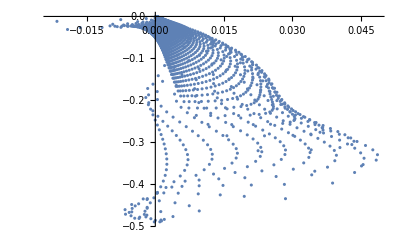

```mathematica
ListPlot[L]
```

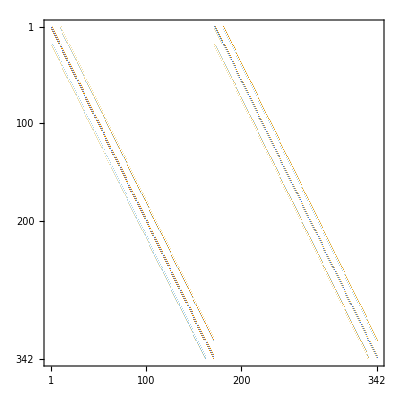
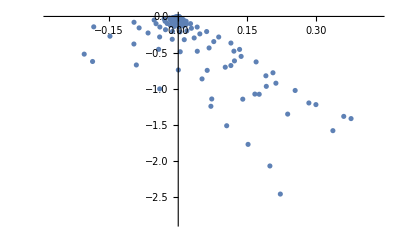
```mathematica
(*Export["20_10test_A.txt",AA]
Export["20_10test_B.txt",BB]
Export["20_10test_Picture.jpg",-Graphics-]
Export["20_10test_Dispersion.jpg",-Graphics-]*)
```

```mathematica
(*liXY = {}
AppendTo[liXY,{2*Subscript[h, r],3*Subscript[h, z]}]
liXY*)
```

```mathematica
Dimensions[liXY]
```

{}

```mathematica
liXY = {};
For[i0= 0,i0≤NN, i0++,
For[j0=0,j0≤M,j0++,AppendTo[liXY,{i0*Subscript[h, r],j0*Subscript[h, z]}]]
]
liXY2=liXY;

For[i2=1,i2≤(NN-1), i2++,
For[j2=1,j2≤(M-1),j2++,
(*{liXY⟦(i2-1)(M-1)+j2⟧,liXY⟦(NN-1)(M-1)+(i2-1)(M-1)+j2⟧} *)liXY2⟦1+i2*(M+1)+j2⟧ = liXY2⟦1+i2*(M+1)+j2⟧+{LS⟦(i2-1)(M-1)+j2⟧,LS⟦(NN-1)(M-1)+(i2-1)(M-1)+j2⟧}]
]

(*liXY3=For[i33=0,i33≤NN,i33++
For[j33=0,j33<M,liXY];*)

(*For[i2=1,i2≤(NN-1), i2++,
For[j2=1,j2≤(M-1),j2++,
(*{liXY⟦(i2-1)(M-1)+j2⟧,liXY⟦(NN-1)(M-1)+(i2-1)(M-1)+j2⟧} *)liXY2⟦1+i2*(M+1)+j2⟧ = liXY2⟦1+i2*(M+1)+j2⟧+{LS⟦(i2-1)(M-1)+j2⟧,LS⟦(NN-1)(M-1)+(i2-1)(M-1)+j2⟧}]
]*)


(*For[i2=1,i2≤Dimensions[liXY], i2++,
If[i>M+1 And i]]*)
Dimensions[liXY]
Dimensions[liXY2]
liXY;
liXY2;
```

{1891,2}

{1891,2}

```mathematica
Mod[62,31]
```

0

```mathematica
liXY;
liXY2;
Dimensions[liXY]
```

{1891,2}

```mathematica
Dimensions[liXY2]
liXY⟦31⟧
liXY2⟦31⟧
```

{1891,2}

{0,4}

{0,4}

```mathematica
{0,4}
Print["1 Номер" ]; 
liXY2⟦1⟧
Print["Номер liXY" M];
liXY⟦M+1⟧
Print["Номер liXY2" M];
liXY2⟦M⟧
Print["Номер liXY" (M+1)];
liXY⟦M+1⟧
Print["Номер liXY2" (M+1)];
liXY2⟦M+1⟧
Print["Номер" (M+2)];
liXY2⟦M+2⟧
Print["Номер"(2M+1)];
liXY2⟦2M+1⟧
Print["Номер" (2M+2)];
liXY2⟦2M+2⟧
Print["Номер"(2M+3)];
liXY2⟦2M+3⟧
Print["Номер"(2M+4)];
liXY2⟦2M+4⟧
Print["Номер"(3M+3)];
liXY2⟦3M+3⟧
```

{0,4}

1 Номер

{0,0}

30 Номер liXY

{0,4}

30 Номер liXY2

{0,58/15}

31 Номер liXY

{0,4}

31 Номер liXY2

{0,4}

32 Номер

{1/6,0}

61 Номер

{0.167903,3.38042}

62 Номер

{1/6,4}

63 Номер

{1/3,0}

64 Номер

{0.338169,0.0408378}

93 Номер

{1/3,4}

```mathematica
(* Задаём границу сетки сверху *)
For[ii=1,ii≤NN,ii++,
For[jj=1,jj≤M+1,jj++, If[Mod[ii*(M+1)+jj,M+1]==0,If[a≤ii*Subscript[h, r]≤b,liXY2⟦ii*(M+1)+jj⟧=liXY⟦ii*(M+1)+jj⟧+{liXY2⟦ii*(M+1)+jj-1⟧⟦1⟧-liXY⟦ii*(M+1)+jj-1⟧⟦1⟧,δ},liXY2⟦ii*(M+1)+jj⟧=liXY2⟦ii*(M+1)+jj⟧+liXY2⟦ii*(M+1)+jj-1⟧-liXY⟦ii*(M+1)+jj-1⟧]]]
]
(*For[ii=0,ii≤NN*M,ii++,
If[Mod[ii,M+1]==0,If[a≤ii*Subscript[h, r]≤b,liXY2⟦ii*M+jj⟧=liXY⟦ii*M+jj⟧+{0,δ},liXY2⟦ii*M+jj⟧=liXY2⟦ii*M+jj⟧+liXY2⟦ii*M+jj-1⟧-liXY⟦ii*M+jj-1⟧]]
]*)
```

```mathematica
Dimensions[L]
```

{1711,2}

```mathematica
L⟦M-1⟧
L⟦M-2⟧
L⟦M-3⟧
```

{0.00123633,-0.48625}

{-0.000977461,-0.483197}

{-0.00206018,-0.478834}

```mathematica
(* Задаём границу сетки слева *)
For[iii=2,iii≤M,iii++, liXY2⟦iii⟧⟦2⟧= liXY2⟦iii⟧⟦2⟧+L⟦iii-1⟧⟦2⟧]
```

```mathematica
(*liXY2⟦1⟧={0,0}*)
liXY2⟦M+1⟧=liXY2⟦M+1⟧+liXY2⟦2M+2⟧-liXY⟦2M+2⟧;
```

```mathematica
Dimensions[liXY]
```

{1891,2}

```mathematica
Dimensions[L]
```

{1711,2}

```mathematica
Dimensions[LS] (* в LS 1711*2 элементов *)
```

{3422}

```mathematica
Print["Номер" 1]; 
liXY2⟦1⟧
Print["Номер" M];
liXY2⟦M⟧
Print["Номер" (M+1)];
liXY2⟦M+1⟧
Print["Номер" (M+2)];
liXY2⟦M+2⟧
Print["Номер"(2M+1)];
liXY2⟦2M+1⟧
Print["Номер" (2M+2)];
liXY2⟦2M+2⟧
Print["Номер"(2M+3)];
liXY2⟦2M+3⟧
Print["Номер"(2M+4)];
liXY2⟦2M+4⟧
Print["Номер"(3M+3)];
liXY2⟦3M+3⟧
```

Номер

{0,0}

30 Номер

{0,3.38042}

31 Номер

{0.00123633,3.51375}

32 Номер

{1/6,0}

61 Номер

{0.167903,3.38042}

62 Номер

{0.167903,3.51375}

63 Номер

{1/3,0}

64 Номер

{0.338169,0.0408378}

93 Номер

{0.33335,3.51285}

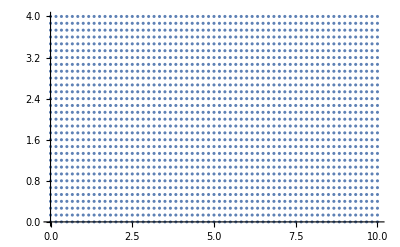

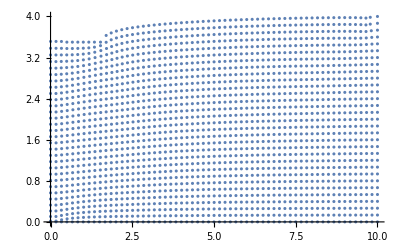

```mathematica
ListPlot[liXY]
ListPlot[liXY2]
(*liXY2*)
```

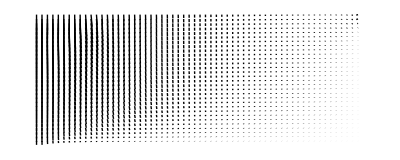

```mathematica
Graphics[MapThread[Line@*List,{liXY,liXY2}]]
```

{}

{31,0}

{31,60,2}

{}

{31,0}

{31,61,2}

{}

{61,0}

{61,31,2}

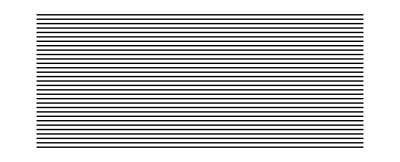

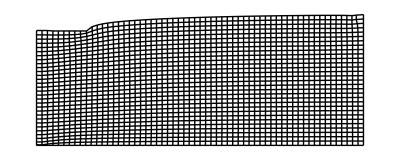

```mathematica
(* строим список для графика линий ДО давления  *)
data= {}
For[i3=0,i3≤M,i3++,AppendTo[data,{}]]
Dimensions[data]
(* соединяем ГОРИЗОНТАЛЬНЫМИ линиями график 2 ДО давления *)
For[i4=0,i4<NN,i4++,
For[j4=1,j4≤M+1,j4++,
AppendTo[data⟦j4⟧,liXY⟦i4*(M+1)+j4⟧]
]
]
Dimensions[data]
(*Graphics[Line/@data]*)


(* строим список для графика линий ПОСЛЕ давления  *)
data2= {}
For[j3=0,j3≤M,j3++,AppendTo[data2,{}]]
Dimensions[data2]

(* соединяем ГОРИЗОНТАЛЬНЫМИ линиями график 2 ПОСЛЕ давления  *)
For[i4=0,i4≤NN,i4++,
For[j4=1,j4≤M+1,j4++,
AppendTo[data2⟦j4⟧,liXY2⟦i4*(M+1)+j4⟧]
]
]
Dimensions[data2]

(* соединяем ВЕРТИКАЛЬНЫМИ линиями график 2 после давления  *)
data3= {}
For[i3=1,i3≤NN+1,i3++,AppendTo[data3,{}]]
Dimensions[data3]

(* соединяем ГОРИЗОНТАЛЬНЫМИ линиями график 2 ПОСЛЕ давления  *)
For[i4=0,i4≤NN,i4++,
For[j4=1,j4≤M+1,j4++,
AppendTo[data3⟦i4+1⟧,liXY2⟦i4*(M+1)+j4⟧]
]
]
Dimensions[data3]
g=Graphics[Line/@data];
g2=Graphics[Line/@data2];
g3=Graphics[Line/@data3];

g
showg1g2 = Show[g2,g3]
```

```mathematica
MatrixPlot[AA];
```

{}

{1711,2}

{1891,2}

{1891,2}

{1891,2}

-Graphics-

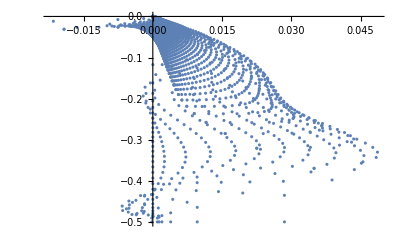

```mathematica
(* Вычисляем Subscript[σ, r],Subscript[σ, z],Subscript[σ, θ] в каждой точке сетки*)
(*Subscript[σ, r][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)Subscript[du, r][i,j]+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+Subscript[dw, z][i,j]))
Subscript[σ, θ][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)toX[Subscript[u, i,j]]/(i*Subscript[h, r])+ν(Subscript[du, r][i,j]+Subscript[dw, z][i,j]))
Subscript[σ, z][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)Subscript[dw, z][i,j]+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+Subscript[du, r][i,j]))*)
(*Subscript[σ, r][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, θ][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)toX[Subscript[u, i,j]]/(i*Subscript[h, r])+ν((1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, z][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])))*)

(* Инициализация списка со всеми перемещениями u и w *)

datauv = {} (* datauv размерности (NN+1)*(M+1) *)

For[iuv=0,iuv≤NN,iuv++,
For[juv =1,juv≤M+1,juv++,
AppendTo[datauv,liXY2⟦iuv*(M+1)+juv⟧-liXY⟦iuv*(M+1)+juv⟧]
]
]
Dimensions[L]
Dimensions[datauv]
Dimensions[liXY]
Dimensions[liXY2]
ListPlot[L]
ListPlot[datauv]
```

Размеры allrlistσ равны {1891,0}

Размеры allθlistσ равны {1891,0}

Размеры allzlistσ равны {1891,0}

Dimensions[allrlistσ]{1891}

Dimensions[allθlistσ]{1891}

Dimensions[allzlistσ]{1891}

Dimensions[liXY2]{1891,2}

График Полный напряжений σ_r

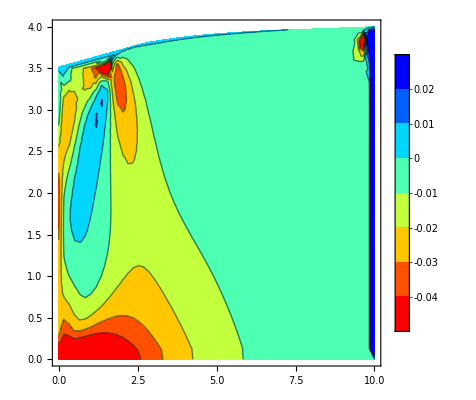

График Полный напряжений σ_θ

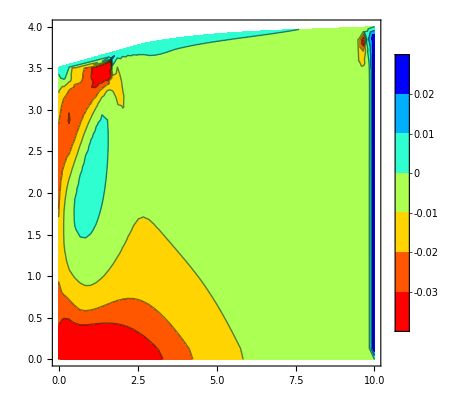

График Полный напряжений σ_z

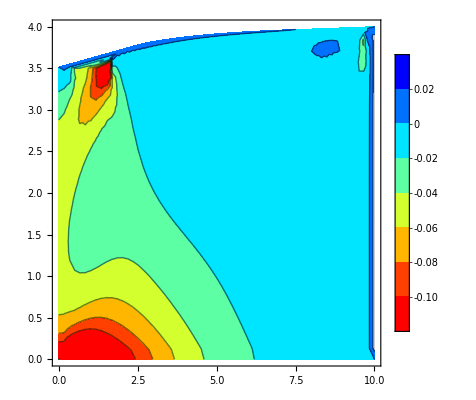

```mathematica
(* Инициализация Subscript[σ, r],Subscript[σ, θ],Subscript[σ, z] в каждой точке (Subscript[u, i,j],Subscript[w, i,j]) *)
(* i,j: i*(M+1)+j+1 *)
(* Размерности rlistσ,θlistσ,zlistσ *)
rlistσ={};
θlistσ={};
zlistσ={};
For[iii=1,iii≤NN-1,iii++,
For[jjj=1,jjj≤M-1,jjj++,{
AppendTo[rlistσ,(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj+1⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj+1⟧⟦1⟧)(*toX[Subscript[u, iii-1,jjj]]*)+ν((datauv⟦iii(M+1)+jjj+1⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+2⟧⟦2⟧(*toX[Subscript[u, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj⟧⟦2⟧)(*toX[Subscript[u, iii,jjj-1]]*)))],
AppendTo[θlistσ,(E(1-2ν))/(1+ν)((1-ν)(datauv⟦iii(M+1)+jjj+1⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+ν((1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj+1⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj+1⟧⟦1⟧(*toX[Subscript[u, iii-1,jjj]]*)) +(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+2⟧⟦2⟧(*toX[Subscript[w, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj⟧⟦2⟧(*toX[Subscript[w, iii,jjj-1]]*))))],
AppendTo[zlistσ,(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+2⟧⟦2⟧(*toX[Subscript[w, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj⟧⟦2⟧(*toX[Subscript[u, iii,jjj-1]]*))+ν((datauv⟦iii(M+1)+jjj+1⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+(1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj+1⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj+1⟧⟦1⟧(*toX[Subscript[u, iii-1,jjj]]*))))]
}
]
]

(* так как у нас в списках rlistσ,θlistσ,zlistσ содержится (M-1)(NN-1) элементов, то создадим списки с (NN+1)*(M+1) элементами, 
	куда в первую очередь поместим элементы из списков rlistσ,θlistσ,zlistσ *)
allrlistσ={};
allθlistσ={};
allzlistσ={};
For[iii=1,iii≤(NN+1)(M+1),iii++,{AppendTo[allrlistσ,{}],AppendTo[allθlistσ,{}],AppendTo[allzlistσ,{}]}]
Print["Размеры allrlistσ равны ",Dimensions[allrlistσ]]
Print["Размеры allθlistσ равны ",Dimensions[allθlistσ]]
Print["Размеры allzlistσ равны ",Dimensions[allzlistσ]]
(* Инициализируем ВСЕ сигмы *)
For[iii=0,iii≤NN,iii++,
For[jjj=1,jjj≤M+1,jjj++,
If[(iii==0) && (jjj ≠1) && (jjj≠ M+1), (* слева *) {allrlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)(ν*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + (1-ν)(1/Subscript[h, r])(-datauv⟦M+1+jjj⟧⟦1⟧)),allθlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)(ν*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + ν(1/Subscript[h, r])datauv⟦M+1+jjj⟧⟦1⟧),
allzlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)((1-ν)*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + ν(1/Subscript[h, r])datauv⟦M+1+jjj⟧⟦1⟧)},
If[(iii≠0)&&(iii≠NN)&& (jjj==1), (* снизу *) 
{allrlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧⟦2⟧,
allθlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧⟦2⟧,
allzlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)(1-ν)(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧⟦2⟧},
If[(iii==NN) && (jjj≠ 1)&& (jjj≠ M+1), (* справа *) 
{allrlistσ⟦NN(M+1)+jjj⟧=(E(1-2ν))/(1+ν)(1-ν)(1/Subscript[h, r])(-datauv⟦(NN-1)(1+M)⟧⟦1⟧),
allθlistσ⟦NN(M+1)+jjj⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, r])(-datauv⟦(NN-1)(1+M)⟧⟦1⟧),
allzlistσ⟦NN(M+1)+jjj⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, r])(-datauv⟦(NN-1)(1+M)⟧⟦1⟧)},
If[(iii≠0)&&(iii≠NN)&& (jjj==M+1 ),(* сверху *)
{allrlistσ⟦iii(M+1)+M+1⟧=(E(1-2ν))/(1+ν)((1-ν)(1/2 Subscript[h, r])(datauv⟦(iii+1)(M+1)+M+1⟧⟦1⟧-datauv⟦(iii-1)(M+1)+M+1⟧⟦1⟧)+ν((1/(iii*Subscript[h, r]))datauv⟦iii(M+1)+M+1⟧⟦1⟧+ (1/Subscript[h, z])(datauv⟦iii(M+1)+M+1⟧⟦2⟧-datauv⟦iii(M+1)+M⟧⟦2⟧))),
allθlistσ⟦iii(M+1)+M+1⟧=(E(1-2ν))/(1+ν)((1-ν)(1/(iii*Subscript[h, r]))datauv⟦iii(M+1)+M+1⟧⟦1⟧+ν((1/2 Subscript[h, r])(datauv⟦(iii+1)(M+1)+M+1⟧⟦1⟧-datauv⟦(iii-1)(M+1)+M+1⟧⟦1⟧)+(1/Subscript[h, z])(datauv⟦iii(M+1)+M+1⟧⟦2⟧-datauv⟦iii(M+1)+M⟧⟦2⟧))),
allzlistσ⟦iii(M+1)+M+1⟧=(E(1-2ν))/(1+ν)((1-ν)(1/Subscript[h, z])(datauv⟦iii(M+1)+M+1⟧⟦2⟧-datauv⟦iii(M+1)+M⟧⟦2⟧)+ν((1/(iii*Subscript[h, r]))datauv⟦iii(M+1)+M+1⟧⟦1⟧+(1/2 Subscript[h, r])(datauv⟦(iii+1)(M+1)+M+1⟧⟦1⟧-datauv⟦(iii-1)(M+1)+M+1⟧⟦1⟧)))},
If[(iii≥ 1) && (iii≤ NN-1) && (jjj≥ 2) &&(jjj≤ M),
{allrlistσ⟦iii(M+1)+jjj⟧=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii-1,jjj]]*))(*toX[Subscript[u, iii-1,jjj]]*)+ν((datauv⟦iii(M+1)+jjj⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+1⟧⟦2⟧(*toX[Subscript[w, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj-1⟧⟦2⟧(*toX[Subscript[u, iii,jjj-1]]*)))),
allθlistσ⟦iii(M+1)+jjj⟧=(E(1-2ν))/(1+ν)((1-ν)(datauv⟦iii(M+1)+jjj⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+ν((1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii-1,jjj]]*)) +(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+1⟧⟦2⟧(*toX[Subscript[w, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj-1⟧⟦2⟧(*toX[Subscript[w, iii,jjj-1]]*)))),
allzlistσ⟦iii(M+1)+jjj⟧=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, z]))(datauv⟦iii(M+1)+jjj+1⟧⟦2⟧(*toX[Subscript[w, iii,jjj+1]]*)-datauv⟦iii(M+1)+jjj-1⟧⟦2⟧(*toX[Subscript[u, iii,jjj-1]]*))+ν((datauv⟦iii(M+1)+jjj⟧⟦1⟧)/(iii*Subscript[h, r])(*toX[Subscript[u, iii,jjj]]*)+(1/(2 Subscript[h, r]))(datauv⟦(iii+1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii+1,jjj]]*)-datauv⟦(iii-1)(M+1)+jjj⟧⟦1⟧(*toX[Subscript[u, iii-1,jjj]]*))))
}]
]
]
]
]
]
]
(* Вычислим напряжения в крайних точках (угловых) *)

(* 
Subscript[σ, r][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, θ][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)toX[Subscript[u, i,j]]/(i*Subscript[h, r])+ν((1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])+(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])))
Subscript[σ, z][i_,j_]:=(E(1-2ν))/(1+ν)((1-ν)(1/(2 Subscript[h, z]))(toX[Subscript[w, i,j+1]]-toX[Subscript[w, i,j-1]])+ν(toX[Subscript[u, i,j]]/(i*Subscript[h, r])+(1/(2 Subscript[h, r]))(toX[Subscript[u, i+1,j]]-toX[Subscript[u, i-1,j]])))
*)

(* нижняя левая *)
(*allrlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)(ν*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + (1-ν)(1/Subscript[h, r])datauv⟦M+1+jjj⟧),allθlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)(ν*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + ν(1/Subscript[h, r])datauv⟦M+1+jjj⟧),
allzlistσ⟦jjj⟧=(E(1-2ν))/(1+ν)((1-ν)*(1/(2 Subscript[h, z])(datauv⟦jjj+1⟧⟦2⟧-datauv⟦jjj-1⟧⟦2⟧)) + ν(1/Subscript[h, r])datauv⟦M+1+jjj⟧)

allrlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧,
allθlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)ν(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧,
allzlistσ⟦iii(M+1)+1⟧=(E(1-2ν))/(1+ν)(1-ν)(1/Subscript[h, z])datauv⟦iii(M+1)+2⟧*)

(* нижняя левая *) (* Subscript[u, 0,j]=0, Subscript[u, i,0]=0, Subscript[w, i,0]=0,Subscript[w, 1,j]=Subscript[w, 0,j] ⇒ Subscript[w, 0,0]=Subscript[w, 1,0]=0 , Subscript[u, 0,0]=0, Subscript[u, 1,0]=0*)
allrlistσ⟦1⟧ = 0; (*(E(1-2ν))/(1+ν)((1-ν)(1/Subscript[h, r])(-datauv⟦M+2⟧⟦1⟧)+ν*(1/Subscript[h, z])(datauv⟦2⟧⟦2⟧-datauv⟦1⟧⟦2⟧));*)
allθlistσ⟦1⟧ = 0;
allzlistσ⟦1⟧ = 0;


(* верхняя левая *)

allrlistσ⟦M+1⟧=(E(1-2ν))/(1+ν)((1-ν)(1/Subscript[h, r])datauv⟦2(M+1)⟧⟦1⟧+ν(1/Subscript[h, z])(datauv⟦M+1⟧⟦2⟧-datauv⟦M⟧⟦2⟧));
allθlistσ⟦M+1⟧=(E(1-2ν))/(1+ν)ν((1/Subscript[h, r])datauv⟦2(M+1)⟧⟦1⟧+(1/Subscript[h, z])(datauv⟦M+1⟧⟦2⟧-datauv⟦M⟧⟦2⟧));
allzlistσ⟦M+1⟧=0;

(* верхняя правая *)

allrlistσ⟦(NN+1)(M+1)⟧=0;
allθlistσ⟦(NN+1)(M+1)⟧=0;
allzlistσ⟦(NN+1)(M+1)⟧=0;

(* нижняя правая *)

allrlistσ⟦NN(M+1)+1⟧=0;
allθlistσ⟦NN(M+1)+1⟧=0;
allzlistσ⟦NN(M+1)+1⟧=0;

(* Построение графика напряжений с границами (новый вариант) *)
Print["Dimensions[allrlistσ]",Dimensions[allrlistσ]];
Print["Dimensions[allθlistσ]",Dimensions[allθlistσ]];
Print["Dimensions[allzlistσ]",Dimensions[allzlistσ]];
Print["Dimensions[liXY2]",Dimensions[liXY2]];
(*liXY2*)
XY2ALLrliσ = {};
XY2ALLθliσ = {};
XY2ALLzliσ = {};
Dimensions[datauv];
(*For[i=1,i≤(M-1)(NN-1),i++, AppendTo[liXY2σ,]]*)

For[iii=0,iii≤NN,iii++,
For[jjj=1,jjj≤M+1,jjj++,
 {AppendTo[XY2ALLrliσ,Join[liXY2⟦iii(M+1)+jjj⟧,{allrlistσ⟦iii*(M+1)+jjj⟧}]],
AppendTo[XY2ALLθliσ,Join[liXY2⟦iii(M+1)+jjj⟧,{allθlistσ⟦iii*(M+1)+jjj⟧}]],
AppendTo[XY2ALLzliσ,Join[liXY2⟦iii(M+1)+jjj⟧,{allzlistσ⟦iii*(M+1)+jjj⟧}]]
}
]
]
(*Print["XY2ALLrliσ = ",XY2ALLrliσ]*)


(* ALL Subscript[σ, r] *)
Print[Style[Полный График напряжений Subscript[σ, r],22,Red]];
Subscript[plotσ, r] = ListContourPlot[XY2ALLrliσ,ClippingStyle->Automatic,PlotLegends->Automatic,PlotLegends->Automatic, ColorFunction->(Blend[{Red,Yellow,Cyan,Blue},#]&)]
(*ListContourPlot[allrlistσ,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[allrlistσ,ColorFunction->"Rainbow",PlotLegends->Automatic]*)
(* ALL Subscript[σ, θ] *)
Print[Style[Полный График напряжений Subscript[σ, θ],22,Red]]
Subscript[plotσ, θ] = ListContourPlot[XY2ALLθliσ,ClippingStyle->Automatic,PlotLegends->Automatic,PlotLegends->Automatic, ColorFunction->(Blend[{Red,Yellow,Cyan,Blue},#]&)]
(*ListContourPlot[allθlistσ,ClippingStyle->Automatic,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[allθlistσ,ClippingStyle->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic]*)


(* ALL Subscript[σ, z] *)
Print[Style[Полный График напряжений Subscript[σ, z],22,Red]];
Subscript[plotσ, z] = ListContourPlot[XY2ALLzliσ,ClippingStyle->Automatic,PlotLegends->Automatic,PlotLegends->Automatic, ColorFunction->(Blend[{Red,Yellow,Cyan,Blue},#]&)]
(*ListContourPlot[allzlistσ,ClippingStyle->Automatic,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[allzlistσ,ClippingStyle->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic]*)
```

Dimensions[rlistσ]

{1711}

Dimensions[θlistσ]

{1711}

Dimensions[zlistσ]

{1711}

График напряжений σ_r

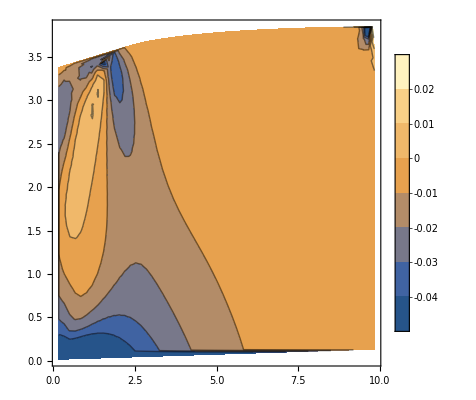

График напряжений σ_θ

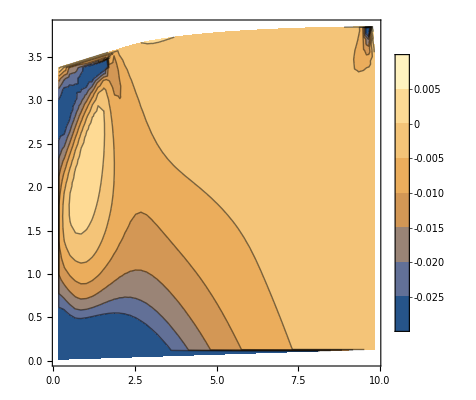

График напряжений σ_z

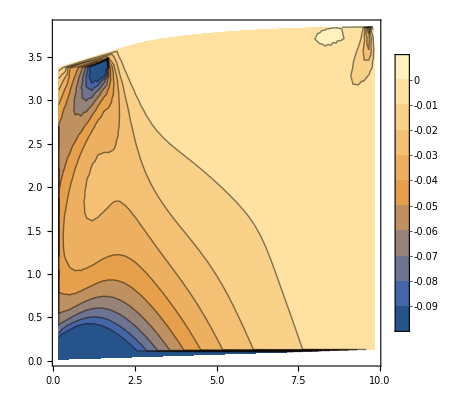

```mathematica
(* Построение графика напряжений без границ (старый вариант) *)

Print["Dimensions[rlistσ]"];Dimensions[rlistσ]
Print["Dimensions[θlistσ]"];Dimensions[θlistσ]
Print["Dimensions[zlistσ]"];Dimensions[zlistσ]
Dimensions[liXY2];
rliXY2σ = {};
θliXY2σ = {};
zliXY2σ = {};
Dimensions[datauv];
(*For[i=1,i≤(M-1)(NN-1),i++, AppendTo[liXY2σ,]]*)

For[iii=1,iii≤NN-1,iii++,
For[jjj=1,jjj≤M-1,jjj++,
 {AppendTo[rliXY2σ,Join[liXY2⟦iii(M+1)+jjj+1⟧,{rlistσ⟦(iii-1)*(M-1)+jjj⟧}]],
AppendTo[θliXY2σ,Join[liXY2⟦iii(M+1)+jjj+1⟧,{θlistσ⟦(iii-1)*(M-1)+jjj⟧}]],
AppendTo[zliXY2σ,Join[liXY2⟦iii(M+1)+jjj+1⟧,{zlistσ⟦(iii-1)*(M-1)+jjj⟧}]]
}
]
]

(* Subscript[σ, r] *)
Print[Style[График напряжений Subscript[σ, r],22,Red]]
ListContourPlot[rliXY2σ,ClippingStyle->Automatic,PlotLegends->Automatic,PlotLegends->Automatic]
(*ListContourPlot[rliXY2σ,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[rliXY2σ,ColorFunction->"Rainbow",PlotLegends->Automatic]*)
(* Subscript[σ, θ] *)
Print[Style[График напряжений Subscript[σ, θ],22,Red]]
ListContourPlot[θliXY2σ,ClippingStyle->Automatic,PlotLegends->Automatic]
(*ListContourPlot[θliXY2σ,ClippingStyle->Automatic,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[θliXY2σ,ClippingStyle->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic]*)


(* Subscript[σ, z] *)
Print[Style[График напряжений Subscript[σ, z],22,Red]]
ListContourPlot[zliXY2σ,ClippingStyle->Automatic,PlotLegends->Automatic]
(*ListContourPlot[zliXY2σ,ClippingStyle->Automatic,ColorFunction->Hue,PlotLegends->Automatic]
ListContourPlot[zliXY2σ,ClippingStyle->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic]*)
```

```mathematica
(*Print["allrlistσ ",allrlistσ]
Print["rlistσ ",rlistσ]
Print["rliXY2σ ",rliXY2σ]*)
```

```mathematica
Export[NotebookDirectory[]~StringJoin~"60_30test_Dispersion.png",showg1g2,ImageResolution->1000]
Export[NotebookDirectory[]~StringJoin~"60_30test_Matrix.png",Rasterize[MatrixPlot[AA],ImageResolution->1000]]
Export[NotebookDirectory[]~StringJoin~"60_30test_points.png",Rasterize[ListPlot[liXY2],ImageResolution->1000]]

Export[NotebookDirectory[]~StringJoin~"60_30voltage_r.png",Rasterize[Subscript[plotσ, r],ImageResolution->1000]]
Export[NotebookDirectory[]~StringJoin~"60_30voltage_θ.png",Rasterize[Subscript[plotσ, θ],ImageResolution->1000]]
Export[NotebookDirectory[]~StringJoin~"60_30voltage_z.png",Rasterize[Subscript[plotσ, z],ImageResolution->1000]]
```

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30test_Dispersion.png

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30test_Matrix.png

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30test_points.png

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30voltage_r.png

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30voltage_θ.png

C:\Users\Rust\Documents\3 курс\6 семестр\курсовая 6 сем\60_30voltage_z.png

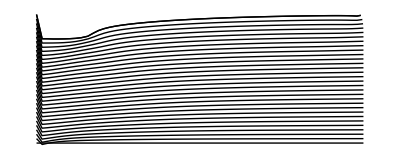
```mathematica
(*Export["60_30test_Matrix.jpg",-Graphics-]
Export["60_30test_Dispersion.jpg",-Graphics-]*)
```